Keine Spinodalinstabilität (alle zweiten Ableitungen positiv).

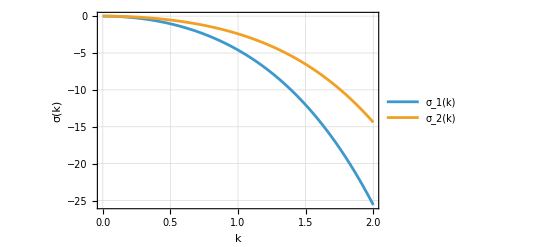

```mathematica
(* ================================================*)(*Zwei-Komponenten-Spinodal nach App.A*)(* ================================================*)(*————Parameter————*)kBT=1.0;      (*in k_B T–Einheiten*)
sigma=1.0;      (*Querschnitt σ im virialen Term*)
cA0=1.0;      (*Gleichgewichts-Konzentration A*)
cB0=1.0;      (*Gleichgewichts-Konzentration B*)
B2AA=2.0;      (*2. Virialkoeff.AA*)
B2BB=2.0;      (*2. Virialkoeff.BB*)
B2AB=1.0;      (*2. Virialkoeff.AB*)
kappaAA=0.5;      (*Gradientenkopplung κ_{AA}*)
kappaBB=0.5;      (*Gradientenkopplung κ_{BB}*)
kappaAB=0.1;      (*Gradientenkopplung κ_{AB}*)
DA=1.0;      (*Diffusionskonstante A*)
DB=1.0;      (*Diffusionskonstante B*)

(*————Freie-Energie-2. Ableitungen————*)
fAA=kBT*(1/cA0+B2AA/sigma);
fBB=kBT*(1/cB0+B2BB/sigma);
fAB=kBT*(B2AB/sigma);

(*————M-Matrix als Funktionen von k————*)
MAA[k_]:=fAA+(kappaAA/sigma)*k^2;
MBB[k_]:=fBB+(kappaBB/sigma)*k^2;
MAB[k_]:=fAB+(kappaAB/sigma)*k^2;
MBA[k_]:=MAB[k];  (*symmetrisch*)

(*————Jacobian J(k) und Eigenwerte σ(k)————*)
Jmat[k_]:=-k^2*{{DA*cA0*MAA[k],DA*cA0*MAB[k]},{DB*cB0*MBA[k],DB*cB0*MBB[k]}};
eigs[k_]:=Eigenvalues[Jmat[k]];  (*{σ1(k),σ2(k)}*)

(*————Bestimme,ob Spinodal-Instabilität vorliegt————*)
spinodalExists=fAA<0||fBB<0||(fAA fBB-fAB^2)<0;
If[!spinodalExists,Print["Keine Spinodalinstabilität (alle zweiten Ableitungen positiv)."];];

(*————k‑Bereich für Plot festlegen————*)
(*Wenn Instabilität,nutze kritische Wellenzahl;sonst fixe Obergrenze*)
kcrit=If[fAA<0,Sqrt[-fAA*sigma/kappaAA],1.0];
kPlotMax=2*kcrit;

(*————Plot der beiden Dispersionen σ₁(k),σ₂(k)————*)
Plot[Evaluate[eigs[k]],{k,0,kPlotMax},Frame->True,(*Rahmenachsen*)FrameLabel->{"k","σ(k)"},(*Beschriftungen*)LabelStyle->Directive[FontSize->14],(*Schriftgröße*)FrameTicksStyle->Directive[FontSize->12],(*Tick‑Schrift*)PlotLegends->Placed[{"σ_1(k)","σ_2(k)"},Above],PlotTheme->"Detailed",GridLines->True]


(*————Finde numerisch k_max der größten Wachstumsrate————*)
dispMax[k_]:=Max[eigs[k]];
(*Suche nur,wenn Instabilität existiert*)
If[spinodalExists,sol=FindMaximum[{dispMax[k],0<k<kPlotMax},{k,kPlotMax/2}];
kmaxVal=k/. sol[[2]];(*extrahiere k->kmaxVal*)lambdaMax=2*Pi/kmaxVal;(*Wellenlänge=2π/k*)Print["k_max       = ",N[kmaxVal,6]];
Print["lambda_max  = ",N[lambdaMax,6]];];
```

Keine Spinodalinstabilität: alle 2. Ableitungen positiv.

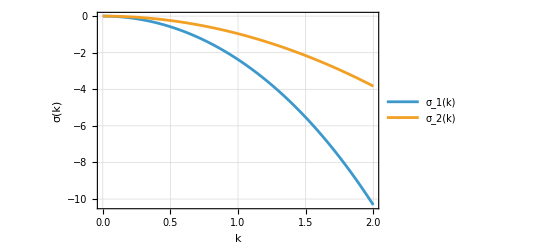

```mathematica
(* ================================================*)(*Zwei-Komponenten-Spinodal mit Partikelradien*)(* ================================================*)(*————Partikelradien (in denselben Längeneinheiten)————*)rA=0.5;     (*Radius von Spezies A*)
rB=0.3;     (*Radius von Spezies B*)

(*————Virialkoeffizienten für harte Kugeln in 3D————*)
(*B2_{ij}=2 π/3 (r_i+r_j)^3*)
B2AA=(2*Pi/3)*(rA+rA)^3;
B2BB=(2*Pi/3)*(rB+rB)^3;
B2AB=(2*Pi/3)*(rA+rB)^3;

(*————Querschnitt σ:hier als geometrische Projektionsfläche AB————*)
sigma=Pi*(rA+rB)^2;

(*————Gradientenkopplungen κ_{ij} (frei wählbar,z.B.proportional zu (r_i+r_j)^2)————*)
kappa0=0.1;                   (*Skalierungsfaktor für κ*)
kappaAA=kappa0*(rA+rA)^2;
kappaBB=kappa0*(rB+rB)^2;
kappaAB=kappa0*(rA+rB)^2;

(*————Sonstige Parameter————*)
kBT=1.0;       (*in k_B T–Einheiten*)
cA0=1.0;       (*Gleichgewichts-Konzentration A*)
cB0=1.0;       (*Gleichgewichts-Konzentration B*)
DA=1.0;       (*Diffusionskonstante A*)
DB=1.0;       (*Diffusionskonstante B*)

(*————Freie-Energie-2. Ableitungen an homog.Zustand————*)
fAA=kBT*(1/cA0+B2AA/sigma);
fBB=kBT*(1/cB0+B2BB/sigma);
fAB=kBT*(B2AB/sigma);

(*————M-Matrix als Funktionen von k————*)
MAA[k_]:=fAA+(kappaAA/sigma)*k^2;
MBB[k_]:=fBB+(kappaBB/sigma)*k^2;
MAB[k_]:=fAB+(kappaAB/sigma)*k^2;
MBA[k_]:=MAB[k];  (*symmetrisch*)

(*————Jacobian J(k) und Eigenwerte σ₁,₂(k)————*)
Jmat[k_]:=-k^2*{{DA*cA0*MAA[k],DA*cA0*MAB[k]},{DB*cB0*MBA[k],DB*cB0*MBB[k]}};
eigs[k_]:=Eigenvalues[Jmat[k]];  (*{σ₁(k),σ₂(k)}*)

(*————Prüfe Spinodalinstabilität————*)
spinodalExists=(fAA<0||fBB<0||(fAA*fBB-fAB^2)<0);
If[!spinodalExists,Print["Keine Spinodalinstabilität: alle 2. Ableitungen positiv."];];

(*————Wellenzahlbereich für Plot————*)
kcrit=If[fAA<0,Sqrt[-fAA*sigma/kappaAA],1.0];
kPlotMax=2*kcrit;

(*————Dispersion plotten————*)
Plot[Evaluate[eigs[k]],{k,0,kPlotMax},Frame->True,FrameLabel->{"k","σ(k)"},LabelStyle->Directive[FontSize->14],FrameTicksStyle->Directive[FontSize->12],PlotLegends->Placed[{"σ_1(k)","σ_2(k)"},Above],PlotTheme->"Detailed",GridLines->True]

(*————Finde k_max und lambda_max (instabler Zweig)————*)
If[spinodalExists,dispMax[k_]=Max[eigs[k]];
sol=FindMaximum[{dispMax[k],0<k<kPlotMax},{k,kPlotMax/2}];
kmaxVal=k/. sol[[2]];
lambdaMax=2*Pi/kmaxVal;
Print["--- Ergebnisse ---"];
Print["k_max       = ",N[kmaxVal,6]];
Print["lambda_max  = ",N[lambdaMax,6]];];
```

```mathematica
(* =================Realspace-Diskretisierung für 2‑Komponenten-Spinodal=================*)(* ——Parameter——*)rA=0.5;rB=0.6;
B2AA=(2*Pi/3)*(rA+rA)^3;
B2BB=(2*Pi/3)*(rB+rB)^3;
B2AB=(2*Pi/3)*(rA+rB)^3;
sigma=Pi*(rA+rB)^2;
kappa0=0.1;
kappaAA=kappa0*(2 rA)^2;
kappaBB=kappa0*(2 rB)^2;
kappaAB=kappa0*(rA+rB)^2;
kBT=1.0;cA0=1.0;cB0=1.0;
DA=1.0;DB=1.0;

(* ——Gitter und Neumann‑Diskretisierung der 2. Ableitung——*)
nPts=50;         (*Zahl der Gitterpunkte*)
L=100.0;      (*Domänenlänge*)
h=L/(nPts-1);

D2=SparseArray[{{1,1}->-1/h^2,{1,2}->1/h^2,{nPts,nPts-1}->1/h^2,{nPts,nPts}->-1/h^2,Band[{2,2}]->ConstantArray[-2/h^2,nPts-2],Band[{2,3}]->ConstantArray[1/h^2,nPts-2],Band[{3,2}]->ConstantArray[1/h^2,nPts-2]},{nPts,nPts}];

D4=D2.D2;  (*4. Ableitung als Quadrat der 2. Ableitung*)

(* ——Hesse‑Matrixelemente f_ab——*)
fAA=kBT*(1/cA0+B2AA/sigma);
fBB=kBT*(1/cB0+B2BB/sigma);
fAB=kBT*(B2AB/sigma);

(* ——Baue Block‑Matrizen J_ab——*)
JAA=DA*cA0*(fAA*D2-(kappaAA/sigma)*D4);
JBB=DB*cB0*(fBB*D2-(kappaBB/sigma)*D4);
JAB=DA*cA0*(fAB*D2-(kappaAB/sigma)*D4);
JBA=DB*cB0*(fAB*D2-(kappaAB/sigma)*D4);

(* ——Gesamte Jacobi‑Matrix 2nPts×2nPts——*)
Jsys=ArrayFlatten[{{JAA,JAB},{JBA,JBB}}];

(* ——Eigenwerte berechnen und sortieren——*)
eigs=Eigenvalues[Jsys];                         (*alle 2*nPts Werte*)
eigsReal=Select[Re[eigs],Im[#]==0&];        (*nur reelle Teile*)
eigsSorted=Reverse@Sort[eigsReal];               (*absteigend*)

(* ——Ausgabe der Top‑10 Wachstumsraten——*)
TableForm[eigsSorted[[1;;Min[10,Length[eigsSorted]]]],TableHeadings->{Range[10],{"σ_i (real space)"}}]
```

1 | -0.000239646
2 | -0.000607252
3 | -0.00215536
4 | -0.00546187
5 | -0.00597908
6 | -0.0116954
7 | -0.015153
8 | -0.0192813
9 | -0.0287062
10 | -0.0296445

Kritisches rB ≈ 11.72

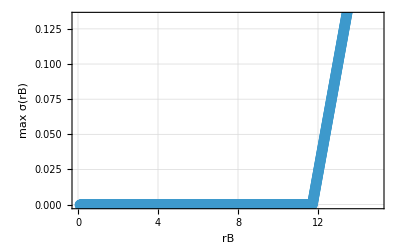

```mathematica
(* ========================================================*)(*Finde kritisches rB,bei dem der größte Eigenwert>0*)(*mit rA=0.1 und rB∈[0.1,0.5] in Schritten von 0.01*)(* ========================================================*)(* ———Globale Einstellungen und Diskretisierung———*)rA=0.1;                          (*fester Radius von A*)
nPts=50;L=100.;h=L/(nPts-1);
(*2. Ableitung mit Neumann-BC*)
D2=SparseArray[{{1,1}->-1/h^2,{1,2}->1/h^2,{nPts,nPts-1}->1/h^2,{nPts,nPts}->-1/h^2,Band[{2,2}]->ConstantArray[-2/h^2,nPts-2],Band[{2,3}]->ConstantArray[1/h^2,nPts-2],Band[{3,2}]->ConstantArray[1/h^2,nPts-2]},{nPts,nPts}];
D4=D2.D2;

(* ———Sonstige feste Parameter———*)
kBT=1.;cA0=1.;cB0=1.;
DA=1.;DB=1.;
kappa0=0.1;

(* ———Sweep über rB und Berechne Max‑Eigenwert———*)
rBvals=Range[0.1,15,0.01];
results=Table[Module[{B2AA,B2BB,B2AB,sigma,kappaAA,kappaBB,kappaAB,fAA,fBB,fAB,JAA,JBB,JAB,JBA,Jsys,sigmaMax},(*Virial‑Koeffizienten aus Radien*)B2AA=(2 Pi/3)*(rA+rA)^3;
B2BB=(2 Pi/3)*(rB+rB)^3;
B2AB=(2 Pi/3)*(rA+rB)^3;
sigma=Pi*(rA+rB)^2;
(*Gradientenkopplungen*)kappaAA=kappa0*(2 rA)^2;
kappaBB=kappa0*(2 rB)^2;
kappaAB=kappa0*(rA+rB)^2;
(*zweite Ableitungen von f0*)fAA=kBT*(1/cA0+B2AA/sigma);
fBB=kBT*(1/cB0+B2BB/sigma);
fAB=kBT*(B2AB/sigma);
(*Block‑Matrizen J_ab*)JAA=DA*cA0*(fAA*D2-(kappaAA/sigma)*D4);
JBB=DB*cB0*(fBB*D2-(kappaBB/sigma)*D4);
JAB=DA*cA0*(fAB*D2-(kappaAB/sigma)*D4);
JBA=DB*cB0*(fAB*D2-(kappaAB/sigma)*D4);
Jsys=ArrayFlatten[{{JAA,JAB},{JBA,JBB}}];
(*größter reeller Eigenwert*)sigmaMax=Max@Select[Re[Eigenvalues[Jsys]],Im[#]==0&];
{rB,sigmaMax}],{rB,rBvals}];

(* ———Kritisches rB finden———*)
crit=First@Select[results,#[[2]]>0&][[1]];
Print["Kritisches rB ≈ ",N[crit,4]];

(* ———Plot:rB vs.größter Eigenwert———*)
ListLinePlot[results,Frame->True,FrameLabel->{"rB","max σ(rB)"},LabelStyle->Directive[FontSize->14],GridLines->Automatic,PlotMarkers->Automatic,PlotTheme->"Detailed"]
```

```mathematica
(* ======================================================*)(*Real‑Space Linearisation gemäß Appendix A des Papers*)(* ======================================================*)(*1) Parameter& Virialkoeffizienten aus Eqs. [A2],[A3]:contentReference[oaicite:0]{index=0}:contentReference[oaicite:1]{index=1}*)RA=0.1;RB=0.2;
B2[i_,j_]:=(4 Pi/3) (i+j)^3;
B3[i_,j_,k_]:=(16 Pi^2/9) (j^3 k^3+3 i j^2 k^2 (j+k)+i^3 (j+k)^3+3 i^2 j k (j^2+3 j k+k^2));

(*2) Querschnitt,Temperaturen,Konzentrationen,Diffusions‑& Cahn–Hilliard‑Koeffizienten*)
sigma=Pi (RA+RB)^2;      (*Eq. [A1] für σ:contentReference[oaicite:2]{index=2}:contentReference[oaicite:3]{index=3}*)
kBT=1.0;
cA0=1.0;cB0=1.0;      (*homogene Basiszustände*)
DA=1.0;DB=1.0;     (*Diffusionskonstanten*)
kappaAA=0.01;kappaBB=0.01;kappaAB=0.005;  (*CH‑Koeffizienten*)

(*3) Freie Energiedichte f0 aus Eq. [A5]:contentReference[oaicite:4]{index=4}:contentReference[oaicite:5]{index=5}*)
f0[cA_,cB_]:=kBT (cA Log[cA]+cB Log[cB]+B2[RA,RA]/(2 sigma) cA^2+B2[RB,RB]/(2 sigma) cB^2+B2[RA,RB]/sigma cA cB+B3[RA,RA,RB]/(6 sigma^2) cA^2 cB+B3[RA,RB,RB]/(6 sigma^2) cA cB^2);

(*4) Hesse‑Matrixelemente f_ab=∂.b2f0/∂c_a∂c_b bei (cA0,cB0):contentReference[oaicite:6]{index=6}:contentReference[oaicite:7]{index=7}*)
fAA=D[f0[cA,cB],cA,cA]/. {cA->cA0,cB->cB0};
fBB=D[f0[cA,cB],cB,cB]/. {cA->cA0,cB->cB0};
fAB=D[f0[cA,cB],cA,cB]/. {cA->cA0,cB->cB0};

(*5) Diskretisierung:2. und 4. Ableitung mit Neumann‑BC auf N Gitterpunkten*)
nPts=50;      (*Anzahl Gitterpunkte*)
L=100.0;   (*Domänenlänge*)
h=L/(nPts-1);

D2=SparseArray[{{1,1}->-1/h^2,{1,2}->1/h^2,{nPts,nPts-1}->1/h^2,{nPts,nPts}->-1/h^2,Band[{2,2}]->ConstantArray[-2/h^2,nPts-2],Band[{2,3}]->ConstantArray[1/h^2,nPts-2],Band[{3,2}]->ConstantArray[1/h^2,nPts-2]},{nPts,nPts}];
D4=D2.D2;  (*Diskretisierte ∂ₓ⁴*)

(*6) Baue die 2×2‑Blockmatrix J_ab nach Eq. [A13]:contentReference[oaicite:8]{index=8}:contentReference[oaicite:9]{index=9}*)
JAA=DA*cA0*(fAA*D2-(kappaAA/sigma)*D4);
JBB=DB*cB0*(fBB*D2-(kappaBB/sigma)*D4);
JAB=DA*cA0*(fAB*D2-(kappaAB/sigma)*D4);
JBA=DB*cB0*(fAB*D2-(kappaAB/sigma)*D4);

(*7) Gesamt‑Jacobi‑Matrix im Realspace (2nPts×2nPts)*)
Jsys=ArrayFlatten[{{JAA,JAB},{JBA,JBB}}];

(*8) Eigenwerte berechnen und ausgeben*)
eigs=Eigenvalues[Jsys];               (*alle 2 nPts Eigenwerte*)
eigsReal=Select[Re[#]&/@eigs,Im[#]==0&];  (*nur reelle*)
eigsSorted=Reverse@Sort[eigsReal];           (*absteigend*)

TableForm[eigsSorted[[1;;Min[10,Length[eigsSorted]]]],TableHeadings->{Range[10],{"σ_i (real space)"}}]
```

1 | -0.000226168
2 | -0.000527563
3 | -0.00203424
4 | -0.00474508
5 | -0.0056436
6 | -0.0110407
7 | -0.0131642
8 | -0.0182054
9 | -0.0257532
10 | -0.0271106

Kritisches rB ≈ 3.5

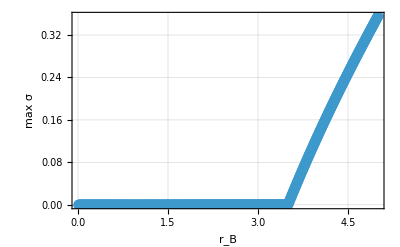

```mathematica
(* ======================================================*)(*Real‑Space Sweep über rB:Größter Eigenwert vs.rB*)(*gemäß Appendix A des Papers:contentReference[oaicite:0]{index=0}:contentReference[oaicite:1]{index=1}*)(* ======================================================*)(*1) Harte‑Kugel Virialkoeffizienten aus Eq. [A2],[A3]*)RA=1;
B2[i_,j_]:=(4 Pi/3)*(i+j)^3;
B3[i_,j_,k_]:=(16 Pi^2/9) (j^3 k^3+3 i j^2 k^2 (j+k)+i^3 (j+k)^3+3 i^2 j k (j^2+3 j k+k^2));

(*2) System‑Parameter und Diskretisierung*)
kBT=1.0;cA0=1.0;cB0=1.0;
DA=1.0;DB=1.0;
kappa0=0.01;
nPts=50;L=100.0;h=L/(nPts-1);
D2=SparseArray[{{1,1}->-1/h^2,{1,2}->1/h^2,{nPts,nPts-1}->1/h^2,{nPts,nPts}->-1/h^2,Band[{2,2}]->ConstantArray[-2/h^2,nPts-2],Band[{2,3}]->ConstantArray[1/h^2,nPts-2],Band[{3,2}]->ConstantArray[1/h^2,nPts-2]},{nPts,nPts}];
D4=D2.D2;

(*3) Sweep über rB und Berechnung des größten Eigenwerts*)
rBList=Range[0.01,5,0.01];
results=Table[Module[{B2AA,B2BB,B2AB,sigma,kappaAA,kappaBB,kappaAB,fAA,fBB,fAB,JAA,JBB,JAB,JBA,Jsys,eigs,eigsReal,maxEig},(*Virialkoeffizienten*)B2AA=B2[RA,RA];
B2BB=B2[rB,rB];
B2AB=B2[RA,rB];
sigma=Pi*(RA+rB)^2;(*Eq. [A1]:contentReference[oaicite:2]{index=2}:contentReference[oaicite:3]{index=3}*)(*Cahn–Hilliard‑Koeffizienten*)kappaAA=kappa0*(2 RA)^2;
kappaBB=kappa0*(2 rB)^2;
kappaAB=kappa0*(RA+rB)^2;
(*Hesse‑Matrixelemente (∂.b2f0)–Eq. [A5]:contentReference[oaicite:4]{index=4}:contentReference[oaicite:5]{index=5}*)fAA=kBT*(1/cA0+B2AA/sigma);
fBB=kBT*(1/cB0+B2BB/sigma);
fAB=kBT*(B2AB/sigma);
(*J‑Blöcke–Eq. [A13]:contentReference[oaicite:6]{index=6}:contentReference[oaicite:7]{index=7}*)JAA=DA*cA0*(fAA*D2-(kappaAA/sigma)*D4);
JBB=DB*cB0*(fBB*D2-(kappaBB/sigma)*D4);
JAB=DA*cA0*(fAB*D2-(kappaAB/sigma)*D4);
JBA=DB*cB0*(fAB*D2-(kappaAB/sigma)*D4);
(*Gesamter Real‑Space Operator*)Jsys=ArrayFlatten[{{JAA,JAB},{JBA,JBB}}];
(*Eigenwerte und größter reeller Anteil*)eigs=Eigenvalues[Jsys];
eigsReal=Select[Re[#]&/@eigs,Im[#]==0&];
maxEig=Max[eigsReal];
{rB,maxEig}],{rB,rBList}];
critData=Select[results,#[[2]]>0&];
If[critData==={},Print["Innerhalb der Range kein positiver Eigenwert gefunden."],crit=First[critData];
Print["Kritisches rB ≈ ",N[crit[[1]],4]];];

(*4) Plot:größter Eigenwert als Funktion von rB*)
ListLinePlot[results,Frame->True,FrameLabel->{"r_B","max σ"},LabelStyle->Directive[FontSize->14],PlotRange->All,PlotMarkers->Automatic,GridLines->True]
```

Eigenvalues::maxit2: Warning: the maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance or use an estimate as a shift, any of which may help.

General::stop: Further output of Eigenvalues::maxit2 will be suppressed during this calculation.

Kritisches rB ≈ 0.00001

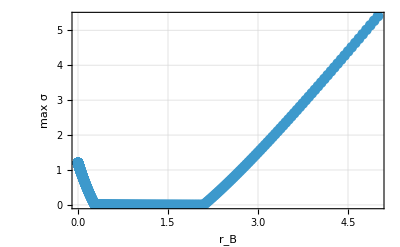

```mathematica
(* ==============================================================*)(*Real‑Space Spinodal Sweep mit korrekter σ_{ij}-Definition*)(*gemäß Appendix A (Eqs.A1,A2,A5,A13) des Papers:contentReference[oaicite:0]{index=0}:contentReference[oaicite:1]{index=1}*)(* ==============================================================*)(*1) Harte‑Kugel Virialkoeffizienten (Eqs. [A2],[A3])*)RA=1.0;
B2[i_,j_]:=(16 Pi/3)*(i+j)^3;

(*2) System‑Parameter& Diskretisierung*)
kBT=1.0;cA0=1.0;cB0=1.0;
DA=1.0;DB=1.0;
kappa0=0.0;
nPts=100;L=100.0;h=L/(nPts-1);
D2=SparseArray[{{1,1}->-1/h^2,{1,2}->1/h^2,{nPts,nPts-1}->1/h^2,{nPts,nPts}->-1/h^2,Band[{2,2}]->ConstantArray[-2/h^2,nPts-2],Band[{2,3}]->ConstantArray[1/h^2,nPts-2],Band[{3,2}]->ConstantArray[1/h^2,nPts-2]},{nPts,nPts}];
D4=D2.D2;

(*3) Sweep über rB und Berechnung des größten Eigenwerts*)
rBList=Exp[Subdivide[Log[0.00001],Log[5.0],1000]];

results=Table[Module[{B2AA,B2BB,B2AB,sigmaAA,sigmaBB,sigmaAB,kappaAA,kappaBB,kappaAB,fAA,fBB,fAB,JAA,JBB,JAB,JBA,Jsys,eigsReal,maxEig},(*Virialkoeffizienten*)B2AA=B2[RA,RA];
B2BB=B2[rB,rB];
B2AB=B2[RA,rB];
(*Geometrische Querschnitte σ_{ij} (Eq.A1)*)sigmaAA=Pi*(RA+RA)^2;
sigmaBB=Pi*(rB+rB)^2;
sigmaAB=Pi*(RA+rB)^2;
(*Cahn–Hilliard‑Koeffizienten κ_{ij}*)kappaAA=kappa0*(2 RA)^2;
kappaBB=kappa0*(2 rB)^2;
kappaAB=kappa0*(RA+rB)^2;
(*Hesse‑Matrixelemente ∂.b2f0/∂c_a∂c_b (Eq.A5)*)fAA=kBT*(1/cA0+B2AA/sigmaAA);
fBB=kBT*(1/cB0+B2BB/sigmaBB);
fAB=kBT*(B2AB/sigmaAB);
(*Jacobi‑Blöcke J_{ab}=D_a c_{a0}[f_{ab} D2-(κ_{ab}/σ_{ab}) D4] (Eq.A13)*)JAA=DA*cA0*(fAA*D2-(kappaAA/sigmaAA)*D4);
JBB=DB*cB0*(fBB*D2-(kappaBB/sigmaBB)*D4);
JAB=DA*cA0*(fAB*D2-(kappaAB/sigmaAB)*D4);
JBA=DB*cB0*(fAB*D2-(kappaAB/sigmaAB)*D4);
(*Gesamte Real‑Space Operator Matrix 2nPts×2nPts*)Jsys=ArrayFlatten[{{JAA,JAB},{JBA,JBB}}];
(*größte reelle Eigenvalue*)(*1 Eigenwert mit größtem Realteil*)(*berechne genau 1 Eigenwert mit größtem Realteil*)maxEig=Re@First@Eigenvalues[Jsys,1,(*genau 1 Eigenwert*)Method->{"Arnoldi","Criteria"->"RealPart",(*nach Realteil sortieren*)"MaxIterations"->5000,(*mehr Iterationen erlauben*)"Tolerance"->1.*^-6,(*geringere Toleranz verlangen*)"BasisSize"->20             (*mehr Basis-Vektoren*)}];


(*4) Kritisches rB bestimmen*)
critData=Select[results,#[[2]]>0&];
If[critData==={},Print["Kein positiver Eigenwert in der Range gefunden."],crit=First[critData];
Print["Kritisches rB ≈ ",N[crit[[1]],4]]];

(*5) Plot:max σ vs.rB*)
ListLinePlot[results,Frame->True,FrameLabel->{"r_B","max σ"},LabelStyle->Directive[FontSize->14],PlotRange->All,PlotMarkers->Automatic,GridLines->True]
```

Eigenvalues::maxit2: Warning: the maximum number of iterations, 5000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance or use an estimate as a shift, any of which may help.

General::stop: Further output of Eigenvalues::maxit2 will be suppressed during this calculation.

Kritisches R_B ≈ 0.00001

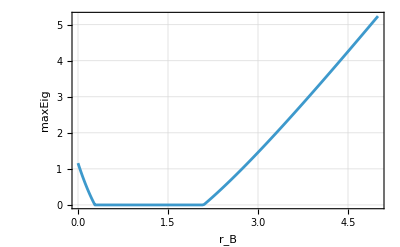

Kritisches R_B ≈ 0.00001

```mathematica
(* ==============================================================*)(*Real‑Space Spinodal Sweep mit korrekter σ_{ij}-Definition*)(*gemäß Appendix A (Eqs.A1,A2,A5,A13) des Papers:contentReference[oaicite:0]{index=0}:contentReference[oaicite:1]{index=1}*)(* ==============================================================*)(*1) Harte‑Kugel Virialkoeffizienten (Eqs. [A2],[A3])*)RA=1.0;
B2[i_,j_]:=(16Pi/3)*(i+j)^3;

(*2) System‑Parameter& Diskretisierung*)
kBT=1.0;cA0=1.0;cB0=1.0;
DA=1.0;DB=1.0;
kappa0=0.0;
nPts=50;L=100.0;h=L/(nPts-1);
D2=SparseArray[{{1,1}->-1/h^2,{1,2}->1/h^2,{nPts,nPts-1}->1/h^2,{nPts,nPts}->-1/h^2,Band[{2,2}]->ConstantArray[-2/h^2,nPts-2],Band[{2,3}]->ConstantArray[1/h^2,nPts-2],Band[{3,2}]->ConstantArray[1/h^2,nPts-2]},{nPts,nPts}];
D4=D2.D2;

(*3) Sweep über rB und Berechnung des größten Eigenwerts*)
rBList=Exp[Subdivide[Log[0.00001],Log[5.0],1000]];

results=Table[Module[{B2AA,B2BB,B2AB,sigmaAA,sigmaBB,sigmaAB,kappaAA,kappaBB,kappaAB,fAA,fBB,fAB,JAA,JBB,JAB,JBA,Jsys,eig},(*Virialkoeffizienten& Sigmas wie gehabt*)B2AA=B2[RA,RA];B2BB=B2[rB,rB];B2AB=B2[RA,rB];
sigmaAA=Pi*(RA+RA)^2;
sigmaBB=Pi*(rB+rB)^2;
sigmaAB=Pi*(RA+rB)^2;
(*kappa0=0 führt automatisch zu kappaAA=0 etc.*)(*Hessian-Matrixelemente*)fAA=kBT*(1/cA0+B2AA/sigmaAA);
fBB=kBT*(1/cB0+B2BB/sigmaBB);
fAB=kBT*(B2AB/sigmaAB);
(*Real-Space Operator Jsys wie gehabt,allerdings mit kappa0=0 fällt der D4-Term weg*)JAA=DA*cA0*(fAA*D2);
JBB=DB*cB0*(fBB*D2);
JAB=DA*cA0*(fAB*D2);
JBA=DB*cB0*(fAB*D2);
Jsys=ArrayFlatten[{{JAA,JAB},{JBA,JBB}}];
(*nur den einen Eigenwert mit größtem Realteil holen*)eig=First@Eigenvalues[Jsys,1,Method->{"Arnoldi","Criteria"->"RealPart","MaxIterations"->5000,"Tolerance"->10.^-8,"BasisSize"->20}];
{rB,Re[eig]}],{rB,rBList}];

(*3) Kritischen Wert extrahieren*)
critData=Select[results,#[[2]]>0&];
If[Length[critData]>0,critRB=critData[[1,1]];
Print["Kritisches R_B ≈ ",N[critRB,4]],Print["Kein Instabilitätsübergang in der Range gefunden."]];

(*4) Plot*)
ListLinePlot[results,Frame->True,FrameLabel->{"r_B","maxEig"},PlotRange->All,GridLines->True]
```